```mathematica
(* Replace IDNumber with your UID *)
Check[SeedRandom[11063430]; 
m=RandomReal[{1,2}],Clear[m];MessageDialog["You must replace ID number with your own student number in the command at the top of the notebook."]]
```

1.24736

```mathematica
(* Defining The Equations *)
equ1={z^(4)-13z^(2)-12z+m==0}
eqn2={x-a m==y,x+m y==b}

(* Solving The Equations *)
Solve[equ1,z]
Solve[eqn2,{x,y}]
```

{1.24736-12 z-13 z^2+z^4==0}

{-1.24736 a+x==y,x+1.24736 y==b}

{{z→-2.96939},{z→-1.11596},{z→0.0943164},{z→3.99104}}

{{x→0.692326 a+0.444967 b,y→-0.555033 a+0.444967 b}}

1.24736 x Cos[x] Sin[1.24736 x]

0.639006

2.74786

10.0912

1.55591 x Cos[x] Cos[1.24736 x]+1.24736 Cos[x] Sin[1.24736 x]-1.24736 x Sin[x] Sin[1.24736 x]

-0.0890027

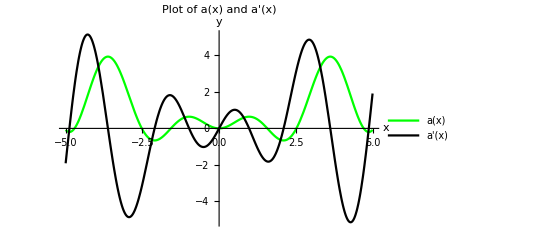

```mathematica
(* Defining The Function *)
a[x_]=m*x*Sin[m*x]*Cos[x]

(* Computing The Function *)
a[1]
a[Pi]

(* Computing The Integral Of The Function *)
Integrate[a[x],{x,-5,5}]

(* Computing The Derivative Of The Function *)
adiff[x_]=D[a[x],x]
adiff[1]

(* Plotting The Functions *)
Plot[{a[x],adiff[x]},{x,-5,5},PlotStyle->{Green,Black},PlotLegends->{"a(x)","a'(x)"},AxesLabel->{"x","y"},PlotLabel->"Plot of a(x) and a'(x)"]
```

{{x→-1.24736},{x→-0.415787},{x→0.},{x→1.24736},{x→1.87104}}

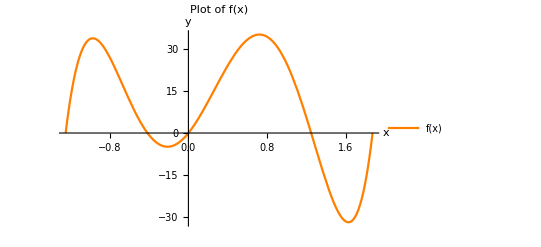

43.5752+163.025 x-252.057 x^2-209.556 x^3+180 x^4

{{x→-0.971853},{x→-0.212195},{x→0.721723},{x→1.62653}}

{0.,-4.44089×10^-15,4.26326×10^-14,-1.13687×10^-13}

{{-0.971853,33.8159},{-0.212195,-4.89514},{0.721723,35.1574},{1.62653,-31.8631}}

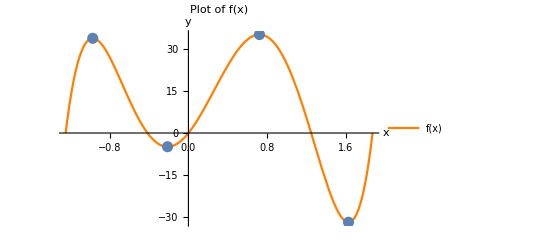

```mathematica
(* Defining The Function *)
f[x_]:=18 m^4 x+42 m^3 x^2-54 m^2 x^3-42 m x^4+36 x^5

(* Solving The Function At y=0 *)
solutions =Solve[f[x]==0,x]

(* Computing The Domain For The Function *)
xmaxrange=Max[x/.solutions];
xminrange=Min[x/.solutions];
p1=Plot[{f[x]},{x,xminrange,xmaxrange},PlotStyle->{Orange},PlotLegends->{"f(x)"},AxesLabel->{"x","y"},PlotLabel->"Plot of f(x)"]

(* Computing The Derivative And It's Solving Them At y=0 *)
fdiff[x_]=D[f[x],x]
sdsolutions=Solve[fdiff[x]==0,x]
fdiff[x/.sdsolutions]

(* Computing The Points *)
points=Transpose[{x/.sdsolutions,f[x/.sdsolutions]}]
p2=ListPlot[points,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"},PlotLabel->"List of points"];
Show[p1,p2]
```

-Graphics-

-Graphics-

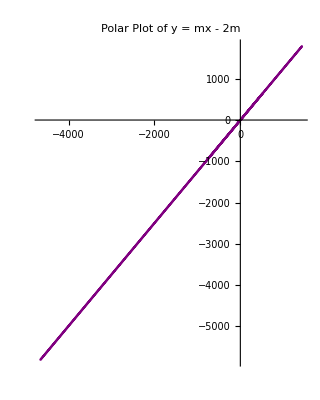

```mathematica
(*define a function for a circle with radius m *)
circle[θ_]=m; 

(*plot the circle using PolarPlot *)
polarp1=PolarPlot[circle[θ],{θ,0,2 Pi},PlotStyle->Green,PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{"Degrees",Automatic},PlotLabel->"Polar Plot of A Circle With Radius M"]

logarithmicspiral[θ_] = m*E^(m*(θ/4)); (*define a function for a logarithmic spiral*)

(*plot the logarithmic spiral using PolarPlot and customize the plot appearance*) 
polarp2 = PolarPlot[
           logarithmicspiral[θ],
           {θ, 0, 100 Pi}, 
           PlotStyle -> Orange, 
           PlotLabel -> "Polar Plot of Logaritmic Spiral"] 

(*define an equation for a straight line*)
straightline=m x-2 m==y; 

(*convert the equation to polar coordinates*)
straightline=straightline/. {x->r Cos[θ],y->r Sin[θ]}; 

(*solve for r in terms of theta*)
straightline=Solve[straightline,r]; 

(*define a function for the polar equation*)
polarstraightline[θ_]:=r/. straightline[[1]]; 

(*plot the straight line using PolarPlot *)
polarp3=PolarPlot[polarstraightline[θ],{θ,0,2 π},PlotStyle->Purple,PlotLabel->"Polar Plot of y = mx - 2m"]
```

```mathematica
k[x_]:=E^Sqrt[m*x+(2/(m*x))];  (*Define function k(x)*)

(*Define two-point formula to approximate the derivative of a function*)
twopointformula[function_,x_,h_]:=(function[x+h]-function[x-h])/(2 h);

(*Define four-point formula to approximate the derivative of a function*)
fourpointformula[function_,x_,h_]:=(8*function[x+h]-8*function[x-h]-function[x+2*h]+function[x-2*h])/(12*h);
precision=5;  (*Set the precision to 5 digits*)

(*Calculate the approximated gradient of k(x) at x=2 using the two-point formula*)
twopointgradient=SetPrecision[twopointformula[k[x],2,0.1],precision];

(*Calculate the approximated gradient of k(x) at x=2 using the four-point formula*)
fourpointgradient=SetPrecision[fourpointformula[k[x],2,0.1],precision];

(*Calculate the actual gradient of k(x) at x=2*)
actualgradient=SetPrecision[Evaluate[D[k[x],x]/. x->2],precision];

errorfunction[a_,b_]:=100*Abs[a-b]/a

(*Calculate the error between the two-point gradient and the actual gradient*)
twopointerror=SetPrecision[errorfunction[twopointgradient,actualgradient],precision];

(*Calculate the error between the four-point gradient and the actual gradient*)
fourpointerror=SetPrecision[errorfunction[fourpointgradient, actualgradient],precision];

(*Print the results with a formatted message*)
Row[{"Two-point Gradient: ",twopointgradient,", Error: ",twopointerror,"%"}]
Row[{"Four-point Gradient: ",fourpointgradient,", Error: ",fourpointerror,"%"}]

(*Print the actual gradient*)
Row[{"Actual Gradient: ",actualgradient}]
```

Two-point Gradient: 5. (-1. 2.7183^(√(1.6034/x+1.2474 x))[1.9]+2.7183^(√(1.6034/x+1.2474 x))[2.1]), Error: (20. Abs[-1.4325+5. (-1. 2.7183^(√(1.6034/x+1.2474 x))[1.9]+2.7183^(√(1.6034/x+1.2474 x))[2.1])])/(-1. 2.7183^(√(1.6034/x+1.2474 x))[1.9]+2.7183^(√(1.6034/x+1.2474 x))[2.1])%

Four-point Gradient: 0.83333 (2.7183^(√(1.6034/x+1.2474 x))[1.8]-8. 2.7183^(√(1.6034/x+1.2474 x))[1.9]+8. 2.7183^(√(1.6034/x+1.2474 x))[2.1]-1. 2.7183^(√(1.6034/x+1.2474 x))[2.2]), Error: (120. Abs[-1.4325+0.83333 (2.7183^(√(1.6034/x+1.2474 x))[1.8]-8. 2.7183^(√(1.6034/x+1.2474 x))[1.9]+8. 2.7183^(√(1.6034/x+1.2474 x))[2.1]-1. 2.7183^(√(1.6034/x+1.2474 x))[2.2])])/(2.7183^(√(1.6034/x+1.2474 x))[1.8]-8. 2.7183^(√(1.6034/x+1.2474 x))[1.9]+8. 2.7183^(√(1.6034/x+1.2474 x))[2.1]-1. 2.7183^(√(1.6034/x+1.2474 x))[2.2])%

Actual Gradient: 1.4325

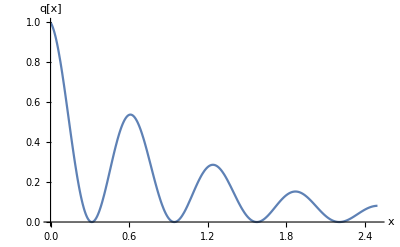

0.462347

0.94497

{0.94497,0.473523,0.466456,0.464536,0.463716,0.463286,0.463032,0.462869}

n | Approximation
4 | 0.94497
8 | 0.473523
12 | 0.466456
16 | 0.464536
20 | 0.463716
24 | 0.463286
28 | 0.463032
32 | 0.462869

1.13079

{1.13079,0.454902,0.603215,0.61013,0.613538,0.61601,0.617923,0.619443}

n | Approximation
4 | 1.13079
8 | 0.454902
12 | 0.603215
16 | 0.61013
20 | 0.613538
24 | 0.61601
28 | 0.617923
32 | 0.619443

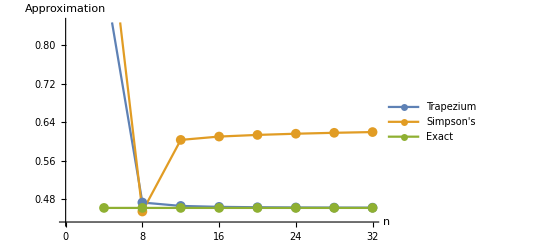

```mathematica
(*Define the function q*)
  q[x_]:=Cos[4*m*x]^2/Exp[x]

(*Plot the integrand over the range of integration*)
Plot[q[x],{x,0,2*m},PlotRange->All,AxesLabel->{"x","q[x]"}]

(*Find the exact value of the integral*)
nint=NIntegrate[q[x],{x,0,2*m}]

(*Implement the Trapezium rule*)
trapeziumRule[function_,a_,b_,n_]:=Module[{h=(b-a)/n},h/2*(function[a]+function[b]+2*Sum[function[a+i*h],{i,1,n-1}])]

(*Use Trapezium rule with n=4 to find an approximate value of the integral*)
trapeziumResult=trapeziumRule[q,0,2*m,4]

(*Tabulate how the result from using the trapezium rule changes as n is increased*)
trapeziumTable=Table[trapeziumRule[q,0,2*m,n],{n,4,32,4}]
TableForm[Transpose[{Range[4,32,4],trapeziumTable}],TableHeadings->{None,{"n","Approximation"}}]

(*Implement Simpson's rule*)
simpsonsRule[function_,a_,b_,n_]:=Module[{h=(b-a)/n},h/3*(function[a]+function[b]+4*Sum[function[a+i*h],{i,1,n/2}]+2*Sum[function[a+(2*i-1)*h],{i,1,n/2-1}])]

(*Use Simpson's rule with n=4 to find an approximate value of the integral*)
simpsonsResult=simpsonsRule[q,0,2*m,4]

(*Tabulate how the values from Simpson's rule change as n is increased*)
simpsonsTable=Table[simpsonsRule[q,0,2*m,n],{n,4,32,4}]
TableForm[Transpose[{Range[4,32,4],simpsonsTable}],TableHeadings->{None,{"n","Approximation"}}]

(*Compare graphically how the two rules converge to nint*)
nValues=Range[4,32,4];
trapeziumValues=trapeziumTable;
simpsonsValues=simpsonsTable;
exactValues=ConstantArray[nint,Length[nValues]];
ListPlot[{Transpose[{nValues,trapeziumValues}],Transpose[{nValues,simpsonsValues}],Transpose[{nValues,exactValues}]},Joined->True,PlotMarkers->{"•",10},PlotLegends->{"Trapezium","Simpson's","Exact"},AxesLabel->{"n","Approximation"}]
```

```mathematica
(*Define The Function*)
g[x_] := m*Sin[2*m*x]^2*Exp[-x/2]



(* plot 3D figure of g revolved about x-axis *)
RevolutionPlot3D[g[x]^2, {x, 0, Pi}, RevolutionAxis -> X, 
 PlotRange -> All, AxesLabel -> {"x", "y", "z"}, 
 PlotLabel -> "Revolution of g[x] about x-axis"]



(* find volume of 3D solid *)
volume = Integrate[Pi*g[x]^2, {x, 0, Pi}]



(* find curved surface area of 3D solid *)
csa = Integrate[2*Pi*g[x]*Sqrt[1 + D[g[x], x]^2], {x, 0, Pi}]
SetPrecision[csa, 3]
```

-Graphics3D-

1.6603